# Taller 1

1) Condición inicial 1: u(x,0)=g(x)

```mathematica
g[x_]:=x*(x-1)*(x-1);
```

Para satisfacer esta condición basta encontrar el desarrollo en serie de Fourier de g(x) :

```mathematica
2*Integrate[g[x]*Sin[Pi*n*x],{x,0,1}]
```

(2 (4 n π+2 n π Cos[n π]-6 Sin[n π]))/(n^4 π^4)

```mathematica
Teniendo en cuenta que seno de nπ es cero, y después de simplificar, se obtiene:
```

```mathematica
Simplify[(2 (4 n π+2 n π Cos[n π]))/(n^4 π^4)]
```

(4 (2+Cos[n π]))/(n^3 π^3)

```mathematica
b[n_]:=(4 (2+Cos[n π]))/(n^3 π^3);
```

El movimiento de la cuerda puede simularse siguiendo los siguientes comandos:

```mathematica
U[x_,t_]:=Sum[(4 (2+Cos[n π]))/(n^3 π^3)*Sin[n*Pi*x]*Cos[Sqrt[49000]*n*Pi*t],{n,10}];
Manipulate[Plot[U[x,t],{x,0,1},PlotRange->{-0.15,0.15}],{t,0,10}]
```

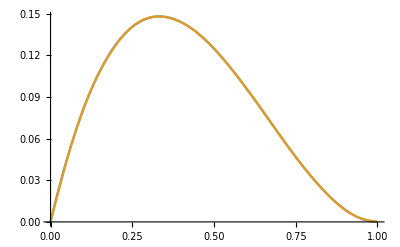

```mathematica
Plot[{x*(x-1)^2,U[x,0]},{x,0,1}]
```

La frecuencia del modo fundamental está dada por

```mathematica
frecuencia fundamental= c/2L
```

(c L)/2

```mathematica
F1=N[Sqrt[49000]/2]
```

110.68

```mathematica
110.67  Hz
```

110.67 Hz

Y las demás frecuencias de los otros modos estarán dados por: n×F1 =n × 110.67 Hz
El primer modo (modo fundamental) entonces resulta ser:

```mathematica
u[x_,t_,n_]:=(4 (2+Cos[n π]))/(n^3 π^3)*Sin[n*Pi*x]*Cos[Sqrt[49000]*n*t];
Primer modo fundamental ;
```

```mathematica
u[x,t,1]
```

(4 Cos[70 √10 t] Sin[π x])/π^3

```mathematica
Segundo Modo fundamental;  u[x,t,2]
```

(3 Cos[140 √10 t] Sin[2 π x])/(2 π^3)

```mathematica
Tercer modo fundamental ;  u[x,t,3]
```

(4 Cos[210 √10 t] Sin[3 π x])/(27 π^3)

```mathematica
Estos pueden graficarse así:
```

```mathematica
Manipulate[Plot[u[x,t,1],{x,0,1},PlotRange->{-0.15,0.15}],{t,0,1}]
Manipulate[Plot[u[x,t,2],{x,0,1},PlotRange->{-0.15,0.15}],{t,0,1}]
Manipulate[Plot[u[x,t,3],{x,0,1},PlotRange->{-0.15,0.15}],{t,0,1}]
```

```mathematica
2) (a) es inmediato, pues:
```

```mathematica
b1 = 2/1 *Integrate[0.05*Sin[Pi*x]*Sin[Pi*x], {x, 0, 1}] = 0.05,   bn = 0,  si n > 0. Luego todos los términos de la serie son cero, excepto el primero, que sería 0.05 Sin[πx]*Cos[1/π π t ]
```

0.05 que sería Cos[t] Sin[πx]

```mathematica
(b)  2*(Integrate[2*x*Sin[n*Pi*x], {x,0,1/2}]+Integrate[2(1-x)*Sin[n*Pi*x],{x,1/2,1}])
```

2 b ((-n π Cos[(n π)/2]+2 Sin[(n π)/2])/(n^2 π^2)+(n π Cos[(n π)/2]+2 Sin[(n π)/2]-2 Sin[n π])/(n^2 π^2))

```mathematica
2*Simplify[(-n π Cos[(n π)/2]+2 Sin[(n π)/2])/(n^2 π^2)+(n π Cos[(n π)/2]+2 Sin[(n π)/2]-2 Sin[n π])/(n^2 π^2)]
```

(2 (4 Sin[(n π)/2]-2 Sin[n π]))/(n^2 π^2)

Teniendo en cuenta que Sin(nπ)=0
(8 Sin[(n π)/2])/(n^2 π^2)

```mathematica
C)
```

```mathematica
2*(Integrate[(3/10)*x*Sin[n*Pi*x], {x,0,1/3}]+Integrate[(3/20)(1-x)*Sin[n*Pi*x],{x,1/3,1}])
```

2 (-(n π Cos[(n π)/3]-3 Sin[(n π)/3])/(10 n^2 π^2)+(2 n π Cos[(n π)/3]+3 Sin[(n π)/3]-3 Sin[n π])/(20 n^2 π^2))

```mathematica
2 (-(n π Cos[(n π)/3]-3 Sin[(n π)/3])/(10 n^2 π^2)+(2 n π Cos[(n π)/3]+3 Sin[(n π)/3]-3 Sin[n π])/(20 n^2 π^2))
```

2 (-(n π Cos[(n π)/3]-3 Sin[(n π)/3])/(10 n^2 π^2)+(2 n π Cos[(n π)/3]+3 Sin[(n π)/3]-3 Sin[n π])/(20 n^2 π^2))

```mathematica
Sabemos que  Sin[n π] = 0; luego, podemos simplificar la expresión
```

expresión la podemos simplificar

```mathematica
2*Simplify[-(n π Cos[(n π)/3]-3 Sin[(n π)/3])/(10 n^2 π^2)+(2 n π Cos[(n π)/3]+3 Sin[(n π)/3])/(20 n^2 π^2)]
```

(9 Sin[(n π)/3])/(10 n^2 π^2)

la Luego sería solución

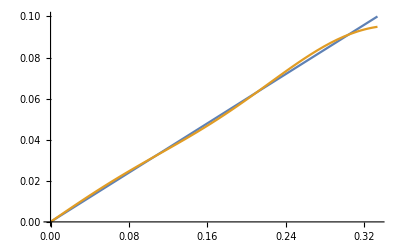

```mathematica
fc[x_]:=3/10*x; fc2[x_]:=3/20*(1-x);
Uc[x_]:=Sum[(9 Sin[(n π)/3])/(10 n^2 π^2)*Sin[n*Pi*x],{n,9}]; Luego la solución sería 
u[x_,t_]:=9/(10 π^2)∑_(n=1)^∞ Sin[(n π)/3]/n^2 Sin[n π] Cos[n t];
Plot[{fc[x],Uc[x]},{x,0,1/3}]
```

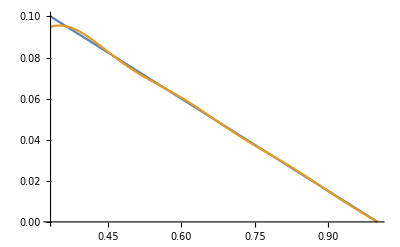

```mathematica
Plot[{fc2[x],Uc[x]},{x,1/3,1}]
```

4)

```mathematica
D[E^(-1*t/2)*(c1*Cos[Sqrt[3]*t/2]+c2*Sin[Sqrt[3]*t/2]),t]
```

ⅇ^(-t/2) (1/2 √3 c2 Cos[(√3 t)/2]-1/2 √3 c1 Sin[(√3 t)/2])-1/2 ⅇ^(-t/2) (c1 Cos[(√3 t)/2]+c2 Sin[(√3 t)/2])

```mathematica
Unset[G]
```

```mathematica
G[t_]:=ⅇ^(-t/2) (1/2 √3 c2 Cos[(√3 t)/2]-1/2 √3 c1 Sin[(√3 t)/2])-1/2 ⅇ^(-t/2) (c1 Cos[(√3 t)/2]+c2 Sin[(√3 t)/2]);
G[0]
```

-c1/2+(√3 c2)/2

```mathematica
U4[x_,t_]:=-(1/Sqrt[3])*Sin[x]*E^(-1*t/2)*(-Sqrt[3]*Cos[Sqrt[3]*t/2]+Sin[Sqrt[3]*t/2]);
```

```mathematica
Manipulate[Plot[U4[x,t],{x,0,Pi},PlotRange->{-1,1}],{t,0,8}]
```